# Projektrapport 2 - Algebra

(Rapportskalet använder sig av ett stylesheet tillverkat av Göran Andersson)

Evan Saboo, Emil Nordin & Perttu Jääskeläinen

## 1. Introduktion: problemformulering

Inom matematikkursen har vi fått i uppgift att lösa två olika matematiska problem med hjälp av Mathematica och dess programmeringsspråk. Målet med den första delporjektet i  är att kunna formulera ett öbestämt linjärt ekvationsystem och finna dess minsta kvadratlösning. Målet med den andra delporjektet är att modellera ett dynamisk system i Mathematica och visualisera systemets dynamik i figurer.

### 1.1 Uppgift 1 - Polynomanpassning med minsta kvadratmetoden

Den första uppgiften går ut på att man ska hitta fjärdegradspolynomet f(t) = a+ b t + c t^2+d t^3+e t^4  som går igenom punkterna (1,1), (2,-1), (3,-59), (-1,5) , (-2,-29), (4, -72) och (-3, 37) med hjälp av minsta kvadratmetoden. Sedan ska man modellera lösningen med de sju punkterna och kolla hur stor residulen är mellan punkterna och lösningen.

### 1.2 Uppgift 2 - Dynamiska system: Ett spel med tal (siffror)

Den andra uppgiften handlar  om tre personer (Kalle, Lisa och David) som spelar ett spel. Spelet går ut på att få ett så högt tal som möjligt efter 1001 omgångar. Varje spelare ska först välja ett reellt tal och ta medelvärdet på de två talen som de andra spelarna valde och erhålla medelvärdet som sitt nya tal. Ett exempel på hu spelet kan förlöpa är:

			Kalle	Lisa	David
Utgångstal		7	11	5
Efter en omgång	8	6	9	
Efter två omgångar	7.5	8.5	7

Den andra uppgiften har tre delfrågor. I den första delfrågan ska man finna matrisen A sådan att  x(t+1)=Ax(t), där vektor x(t)=(a
b
c), a=a(t), b=b(t) och c=c(t). Vektorn beror av den diskreta tiden t.

Den andra deluppgiften går ut på att använda utgångstalen 7, 11 och 5 som i exemplet ovan och kolla vad ställningen är efter 10 omgångar, samt efter 50 omgångar.

I den sista deluppgiften ska man ränka ut vad ställnningen är då Kalle och Lisa har utgångstalen 1 respiktive 2 medan David väljer ett utgångstal d. Man ska ta fram ett slutet uttryck för för a(t), b(t) och c(t) för att lösa uppgiften. Med hjälp av lösningen ska man kolla för vilka d David kommer att vinna spelet efter t omgångar.

## 2 Genomförande och härledningar

### 2.1 Uppgift 1 - Polynomanpassning med minsta kvadratmetoden

#### a)

Först använde vi datatypen ClearAll för att rensa alla globala variblar från dess värden, sedan tilldelade vi den generalla frjärdegradspolynomet till f(t) för att kunna förenkla funktionen med bestämda punkter . Efter att ha förenklat alla punkter med sin egen funktion tilldelades lösningarna till matrisen p.

```mathematica
ClearAll["`*"]
```

```mathematica
x1:=1
x2:=2
x3:=3
x4:=4
x5:=-1
x6:=-2
x7:=-3
```

```mathematica
y1:=1
y2:=-1
y3:=-59
y4:=-72
y5:=5
y6:=-29
y7:=37
```

```mathematica
f[t_]:=a+ b*t +c*t^2+d*t^3+e*t^4
```

```mathematica
f[x1]==y1
```

a+b+c+d+e==1

```mathematica
f[x2]==y2
```

a+2 b+4 c+8 d+16 e==-1

```mathematica
f[x3]==y3
```

a+3 b+9 c+27 d+81 e==-59

```mathematica
f[x4]==y4
```

a+4 b+16 c+64 d+256 e==-72

```mathematica
f[x5]==y5
```

a-b+c-d+e==5

```mathematica
f[x6]==y6
```

a-2 b+4 c-8 d+16 e==-29

```mathematica
f[x7]==y7
```

a-3 b+9 c-27 d+81 e==37

```mathematica
p:={
{1,1,1,1,1,1},
{1,2,4,8,16,-1},
{1,3,9,27,81,-59},
{1,4,16,64,256,-72},
{1,-1,1,-1,1,5}, 
{1,-2,4,-8,16,-29},
{1,-3,9,-27,81,37}
}
```

Efter att ha tilldelat lösningarna till matrisen p använde vi  Mathematica funktionen MatrixForm för att visa matrisen på matrisform.
Vi ser nedan att matrisen dimension är 7x6 där den har 7 rader och 6 columner. Utan att inkludera svaren så blir matrisens dimension till 7x5.

```mathematica
MatrixForm[p]
```

(1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | -1
1 | 3 | 9 | 27 | 81 | -59
1 | 4 | 16 | 64 | 256 | -72
1 | -1 | 1 | -1 | 1 | 5
1 | -2 | 4 | -8 | 16 | -29
1 | -3 | 9 | -27 | 81 | 37)

Vi använde funktionen RowReduce för att reducera matrisen p men vi fick ett ogilligt svar eftersom Reduced Row Echelon Form metoden inte funkar med ojämna dimensioner.

```mathematica
RowReduce[p]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0)

#### b)

För att hitta fjärdegradspolynomet f(t) = a+ b t + c t^2+d t^3+e t^4 använde vi minsta kvadratmetoden på två olika sätt.
Det första sättet utfördes med hjälp av minst kvadratformlen A^T*A =A^T* B där A och B är matriser som är uppdelade från matrisen p. A^T är den transponata matrisen av matrisen A.

```mathematica
A:={
{1,1,1,1,1},
{1,2,4,8,16},
{1,3,9,27,81},
{1,4,16,64,256},
{1,-1,1,-1,1},
{1,-2,4,-8,16},
{1,-3,9,-27,81}
}
```

```mathematica
B :={{1},{-1},{-59},{-72},{5},{-29},{37}}
```

```mathematica
MatrixForm[A]
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16
1 | 3 | 9 | 27 | 81
1 | 4 | 16 | 64 | 256
1 | -1 | 1 | -1 | 1
1 | -2 | 4 | -8 | 16
1 | -3 | 9 | -27 | 81)

```mathematica
MatrixForm[B]
```

(1
-1
-59
-72
5
-29
37)

```mathematica
AT:=Transpose[A]
```

```mathematica
MatrixForm[AT]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | -1 | -2 | -3
1 | 4 | 9 | 16 | 1 | 4 | 9
1 | 8 | 27 | 64 | -1 | -8 | -27
1 | 16 | 81 | 256 | 1 | 16 | 81)

```mathematica
MatrixForm[AT.A]
```

(7 | 4 | 44 | 64 | 452
4 | 44 | 64 | 452 | 1024
44 | 64 | 452 | 1024 | 5684
64 | 452 | 1024 | 5684 | 16384
452 | 1024 | 5684 | 16384 | 79172)

```mathematica
MatrixForm[AT.B]
```

(-118
-524
-1464
-6980
-20688)

Efter att ha använt minsta kvadratformeln kombinerade vi matrsien A och B tillsammans till en ny matris som vi kallade för “AB” .

```mathematica
AB:={
{7,4,44,64,452,-118},
{4,44,64,452,1024,-524},
{44,64,452,1024,5684,-1464},
{64,452,1024,5684,16384,-6980},
{452,1024,5684,16384,79172,-20688}
}
```

```mathematica
MatrixForm[AB]
```

(7 | 4 | 44 | 64 | 452 | -118
4 | 44 | 64 | 452 | 1024 | -524
44 | 64 | 452 | 1024 | 5684 | -1464
64 | 452 | 1024 | 5684 | 16384 | -6980
452 | 1024 | 5684 | 16384 | 79172 | -20688)

Nu kan man se att matrisen AB har jämna antal rader och kolumner (om man inte inkluderar den sista kolumen ), då kan vi använda Mathematica funktionen RowReduce för att hitta fjärdegradspolynomet  f(t).

```mathematica
MatrixForm[RowReduce[AB]]//N
```

(1. | 0. | 0. | 0. | 0. | 14.0098
0. | 1. | 0. | 0. | 0. | 14.5718
0. | 0. | 1. | 0. | 0. | -11.4085
0. | 0. | 0. | 1. | 0. | -3.27913
0. | 0. | 0. | 0. | 1. | 0.967886)

Genom att använda Mathematica funktionen LeastSquares fick vi samma svar som minsta kvadratformeln. Detta var den andra sättet att hitta funktionen f(t).

```mathematica
{a,b,c,d,e}=LeastSquares[A,B]//N
```

{{14.0098},{14.5718},{-11.4085},{-3.27913},{0.967886}}

```mathematica
f[t]
```

{14.0098+14.5718 t-11.4085 t^2-3.27913 t^3+0.967886 t^4}

Vi kontrollerade också fjärdegradspolynomtet genom återsubstitution och fick resultaten nedan:

```mathematica
{Y1}=y/.Solve[f[x1]==y,y]
```

{14.8618}

```mathematica
{Y2}=y/.Solve[f[x2]==y,y]
```

{-13.2276}

```mathematica
{Y3}=y/.Solve[f[x3]==y,y]
```

{-55.0894}

```mathematica
{Y4}=y/.Solve[f[x4]==y,y]
```

{-72.3252}

```mathematica
{Y5}=y/.Solve[f[x5]==y,y]
```

{-7.72358}

```mathematica
{Y6}=y/.Solve[f[x6]==y,y]
```

{-19.0488}

```mathematica
{Y7}=y/.Solve[f[x7]==y,y]
```

{34.5528}

```mathematica
Point1:={{x1,y1},{x2,x2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},{x7,y7}}
```

```mathematica
Point2:={{x1,Y1},{x2,Y2},{x3,Y3},{x4,Y4},{x5,Y5},{x6,Y6},{x7,Y7}}
```

Efter att ha hittat funktionen f(t) var det dags att använda Mathematica funktionen Plot för att modellera f(t) med de gamla och de nya punkterna.

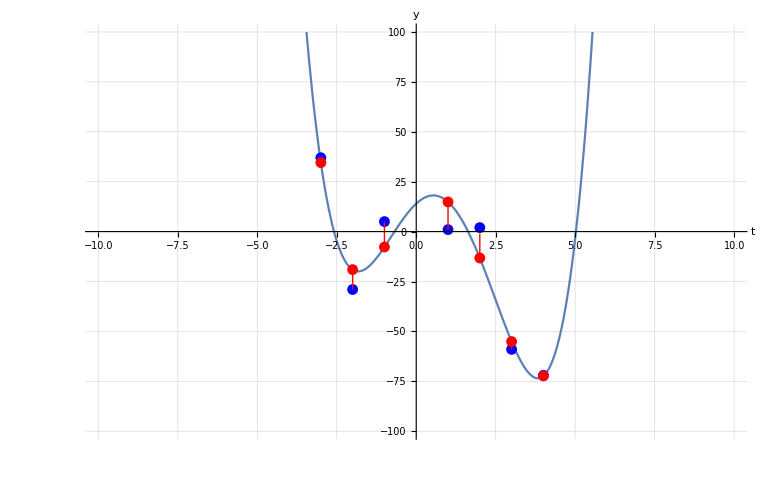

```mathematica
Plot[f[t], {t, -10, 10}, AxesLabel -> {t,y},
PlotRange->{-100,100}, LabelStyle->(FontSize->16), GridLines->Automatic,Epilog->{PointSize[0.01],Blue,Point[Point1],Red,Point[Point2],
Line[{{{x1,y1},{x1,Y1}},{{x2,y2},{x2,Y2}},{{x3,y3},{x3,Y3}},{{x4,y4},{x4,Y4}},{{x5,y5},{x5,Y5}},{{x6,y6},{x6,Y6}},{{x7,y7},{x7,Y7}}}]}]
```

#### c)

I sista deluppgiften kollade vi hur stor residualen är mellan de gamla punkterna och kvadratlsöningen f(t) med hjälp av Mathematica funktionen EuclodeanDistance, som tog avståndet mellan de gamla och de nya punkterna.

```mathematica
r1=EuclideanDistance[{x1,y1},{x1,Y1}]
```

13.8618

```mathematica
r2=EuclideanDistance[{x2,y2},{x2,Y2}]
```

12.2276

```mathematica
r3=EuclideanDistance[{x3,y3},{x3,Y3}]
```

3.91057

```mathematica
r4=EuclideanDistance[{x4,y4},{x4,Y4}]
```

0.325203

```mathematica
r5=EuclideanDistance[{x5,y5},{x5,Y5}]
```

12.7236

```mathematica
r6=EuclideanDistance[{x6,y6},{x6,Y6}]
```

9.95122

```mathematica
r7=EuclideanDistance[{x7,y7},{x7,Y7}]
```

2.44715

Normen av det kvadratiska felet är:

```mathematica
(r1+r2+r3+r4+r5+r6+r7)/7
```

7.92102

### 2.2 Uppgift 2 - Dynamiska system: Ett spel med tal (siffror)

#### a)

För att få fram matrisen A så att x(t+1)=Ax(t) var det bara att tänka såhär:

a    b    c
a = (b+c)/2  =  (0, 0.5, 0.5) 
b = (a+c)/2  =  (0.5, 0, 0.5) 
c = (a+b)/2  =  (0.5, 0.5, 0)

a = (b+c)/2  = b/2 + c/2 = (a*0 + b*0.5 + c*0.5)
b = (a+c)/2  = a/2 + c/2 = (a*0.5 + b*0 + c*0.5) 
c = (a+b)/2  = a/2 + b/2 = (a*0.5 + b*0.5 + c*0)

=  (a*0 + b*0.5 + c*0.5), (a*0.5 + b*0 + c*0.5), (a*0.5 + b*0.5 + c*0)

```mathematica
ClearAll["`*"]
```

```mathematica
A:={{0,0.5,0.5},{0.5,0,0.5},{0.5,0.5,0}}
```

```mathematica
MatrixForm[A]
```

(0 | 0.5 | 0.5
0.5 | 0 | 0.5
0.5 | 0.5 | 0)

#### b)

I den andra deluppgiften tilldelade vi formeln  Ax(t) till funktionen x(t+1)sådan att det blev x(t)= Ax(t-1). För att få funktionen att funka gav vi den vektorn {5,11,7} som startvektor. Till slut kunde vi få ut spelets ställning efter 10 och 50 omgångar.

```mathematica
x[t_]:=x[t]=A.x[t-1]
```

```mathematica
x[0]:={5,11,7}
```

```mathematica
x[10]
```

{7.66406,7.66992,7.66602}

```mathematica
x[50]
```

{7.66667,7.66667,7.66667}

#### c)

I den sista deluppgiften gick vi utifrån Av = λv för att lösa uppgiften, där λ är egenvärde och v är egenvektor. Först fick vi ut egenvärden  med Mathematica funktionen Eigenvalues, eller  med funktion Det[A - λ*I] = 0 där I är en identitetsmatris.

```mathematica
Clear[x]
```

```mathematica
Eigenvalues[A]
```

{1.,-0.5,-0.5}

```mathematica
f[λ]=Det[A-λ*IdentityMatrix[3]]
```

0.25+0.75 λ-λ^3

```mathematica
{λ3,λ2,λ1}=λ/.Solve[f[λ]==0,λ]
```

{-0.5,-0.5,1.}

Efter att ha löst ut ut funktionen  f[λ]=0.25+0.75 λ-λ^3 med Solve fick vi egenvärden λ1 = 1 , λ2 = -0.5 och λ3 = -0.5.

Nu var det dags att lösa ut tre egenvektorer eftersom vi fick 3 egenvärden. Vi ladde in varje egenvärde i sin egen matris Eg och och använde funktionen RowReduce för att rad reducera varje matris.

```mathematica
g[λ_]=A-λ*IdentityMatrix[3]
```

{{-λ,0.5,0.5},{0.5,-λ,0.5},{0.5,0.5,-λ}}

```mathematica
Eg:={{0-λ,0.5,0.5,0},{0.5,0-λ,0.5,0},{0.5,0.5,0-λ,0}}
```

```mathematica
λ:=-0.5
```

```mathematica
RowReduce[Eg]//MatrixForm
```

(1 | 1. | 1. | 0.
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Då λ =-0.5 fick vi att:
x + y + z = 0
y = a
z = b 
där z och y är fria tal. Till slut kom vi fram till att v = (x = -y -z
y = a
z = b) → (-a -b
a
b) → (-a 
a
0)+ (-b
0
b)→  a*(-1 
1
0)+ b*(-1
0
1), där a och b skalar upp vektorerna.

```mathematica
λ:=1
```

```mathematica
RowReduce[Eg]//MatrixForm
```

(1 | 0. | -1. | 0.
0 | 1 | -1. | 0.
0 | 0 | 0 | 0)

Då λ =1 fick vi att:
x - z = 0
y + z = 0
z = a 
där z är en fri värde. Efter fick vi att v = (x = z
y = z
z = a) → (a
a
a) → +  a*(1
1
1) där a skalar upp vektorerna.

Vi kom fram till att egenvektorerna blev:

```mathematica
v1:={1,1,1}
```

```mathematica
v2:={-1,1,0}
```

```mathematica
v3:={-1,0,1}
```

Egenvektorerna användes sen i formeln x[0] = c1*v1 + c2*v2 + c3*v3 för att lösa ut konstanterna c1, c2 och c3 med hjälp av Mathematica funktionen Solve.

```mathematica
x[0]:={1,2,0.5}
```

```mathematica
{{c1,c2,c3}}={c1,c2,c3}/.Solve[c1*v1+c2*v2+c3*v3==x[0]]
```

{{1.16667,0.833333,-0.666667}}

Vi vet att x[0] = c1*v1 + c2*v2 + c3*v3 och A = λ så vi kan kom fram till att
 x[t] = A^t*x[0] = c1*λ1^t*v1 + c2*λ2^t*v2 + c3*λ3^t*v3, vilket är slut utrycket för vektorn x[t] ={a[t], b[t], c[t]}.

```mathematica
x[t_]:=c1*λ1^t*v1+c2*λ2^t*v2+c3*λ3^t*v3
```

Vi prövade med olika tider t  och olika värden d och kom fram till att david vinner då 1 > d > 2 varannan runda (varannan t).

```mathematica
x[1]
```

{1.25,0.75,1.5}

```mathematica
x[2]
```

{1.125,1.375,1.}

```mathematica
x[3]
```

{1.1875,1.0625,1.25}

```mathematica
x[10]
```

{1.1665,1.16748,1.16602}

```mathematica
x[15]
```

{1.16667,1.16664,1.16669}

## 3. Resultat och slutsats

### 3.1 Uppgift 1 - Polynomanpassning med minsta kvadratmetoden

#### a)

I första deluppgiften fick vi matrisen (1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | -1
1 | 3 | 9 | 27 | 81 | -59
1 | 4 | 16 | 64 | 256 | -72
1 | -1 | 1 | -1 | 1 | 5
1 | -2 | 4 | -8 | 16 | -29
1 | -3 | 9 | -27 | 81 | 37)och kom fram till att matrisens dimension är 7x6 där matrisen har 7 rader och 6 kolumner. Om man inte inkluderar svaren till fjärdegradpolynomet f(t) blir matrisens dimension 7x5.

#### b)

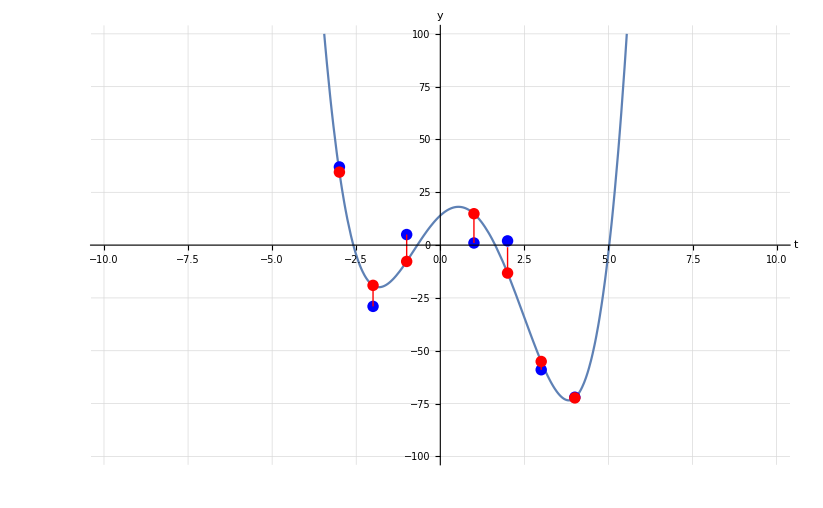
Genom att använda både Mathematica funktionen LeastSquares och minsta kvadratformeln A^T*A =A^T* B fick vi samma resultat:

(1. | 0. | 0. | 0. | 0. | 14.0098
0. | 1. | 0. | 0. | 0. | 14.5718
0. | 0. | 1. | 0. | 0. | -11.4085
0. | 0. | 0. | 1. | 0. | -3.27913
0. | 0. | 0. | 0. | 1. | 0.967886)
Efter att ha löst matrisen fick vi minsta kvadratlösningen till fjärdegradspolynomet: 

f(t)=14.0098+14.5718 t-11.4085 t^2-3.27913 t^3+0.967886 t^4

Nedan ser vi modelleringen av funktionen f(t) med alla gamla och nya punkter och vi kan också se residualen mellan dem.
-Graphics-

Meningen med minsta kvadratmetoden är att vi ska få en funktion f(t) som är går “närmast” igenom alla punkterna (1,1), (2,-1), (3,-59), (-1,5) , (-2,-29), (4, -72) och (-3, 37). Eftersom antalet punkter var större än antalet fria parametrar i funktion f(t) kunde man inte finna funktionen med hjälp Reduced Row Echelon Form.

#### c)

I sista deluppgiften räknade vi ut residualen mellan de gamla punkterna och den nya fjärdegradspolynomet f(t) genom att räkna ut avståndet mellan de gamla punkterna och de nya punkterna. Man kan se att ju större x-koordinaten blir desto mindre blir residualen, samma sak gäller för alla negativa x-koordinater.

Old Points | New Points | Distance
{1,1} | {1,14.86} | 13.86
{2,-1} | {2,-13.23} | 12.23
{3,-59} | {3,-55.09} | 3.91
{4,-27} | {4,-72.24} | 0.33
{-1,5} | {-1,-7.72} | 12.72
{-2,-29} | {-2,-19.05} | 9.95
{-3,37} | {-3,34.55} | 2.45

Normen av det kvadratiska felet är 7.92102.

### 3.2 Uppgift 2 - Dynamiska system: Ett spel med tal (siffror)

#### a)

I första deluppgiften fann vi matrisen A sådan att x(t+1)=Ax(t), där x[t] måste ha ett startvärde för att funktionen ska funka.

(0 | 0.5 | 0.5
0.5 | 0 | 0.5
0.5 | 0.5 | 0)

#### b)

Vi använde utgångstalen 7, 11 och 5 och fick:

Omgång | Ställning
10 | {7.6640625,7.6699219,7.6660156}
50 | {7.6666667,7.6666667,7.6666667}

Vi kom fram till att efter varje omgång kommer de tre olika angivnga talen att gå närmare medlevärdet av de tre första utgångstalen dvs. (a+b+c)/2  . I detta fall är medelvärdet av 7, 11 och 5 ungefär 7.6667.

#### c)

Vi kom fram till att David måste ha ett värde som är större än två eller mindre än ett för att han ska vinna varannan runda. Om david väljer ett tal mindre än ett kommer han att vinna varannan runda där tiden t är en ojämn heltal. Om han väljer ett tal som är större än två kommer han att vinna alla jämna rundor, dvs. tiden t är en jämn heltal. 
Vi fick ut att egenvärdena blev λ1 = 1, λ2= -0.5 och λ3 = -0.5, och egenvektorer blev v1 = (1
1
1) , v2 = (-1 
1
0) och v3 = (-1 
0
1). Det ledde till att vi löste ut konstanterna c1, c2, c3 i formeln x[0] = c1*v1 + c2*v2 + c3*v3, där x[0] = {1, 2, 0.5}. Eftersom A = λ kom vi fram till att 
x[t] = A^t*x[0] = c1*λ1^t*v1 + c2*λ2^t*v2 + c3*λ3^t*v3.
Om man använder Mathematica funktion Limit och tiden t går emot oändlighet får man:

```mathematica
Limit[x[t],t->Infinity]
```

{1.16667,1.16667,1.16667}

Eftersom tiden t går mot oändligheten kommer bara λ1^t att vara kvar, då λ2^t  och λ3^t går mot 0 och slutfunktionen blir
x[t] = A^t*x[0] = c1*λ1^t*v1. 
Vi får till slut att a = b = c, dvs Kalles, Lisas och Davids tal blir lika med medelvärdet av deras första utgångstal ( (a[0] + b[0] + c[0])/3 ).

### Slutsats

Projketet gav oss bra kunskap inom algerbraiska operationer och linjär algebra.
Under detta projekt har vi utvidgat våra kunskaper inom Mathematica. Detta genom att hitta  lösningen till ett överbestämt linjät evkationsystem med hjälp minsta kvadratmetoden i Mathematica , vad residual betyder och hur den förändras i en funktion. Vi har också lärt oss flera Mathematica funktioner som LeastSquares och EuclodeanDistance  samt hur funktionen Plot fungerar med andra funktioner. Projektet gav oss en del kunskap om hur dynamisk system funkar och hur vi kan få fram ett fungerande funktion till medlevärdet av tre reella tal.

Matte föreläsningar och övningar hjälpte oss mycket med att lösa alla uppgifter i projekt 2. Vi kommer forstätta att använda Mathematica till framtida matte projekter och för att lösa svåra matteuppgifter.